```mathematica
2-2
```

0

```mathematica
g[x_]:=1/(√(2π)σ)ⅇ^(-x^2/(2 σ^2))
```

```mathematica
N[g(.5)]
```

0.5 g

```mathematica
σ = 2
```

2

```mathematica
1
```

1

```mathematica
N[g[{-3,-2.5,-2,-1.5,-1,-.5,0,.5,1,1.5,2,2.5,3}]]
```

{0.0647588,0.0913245,0.120985,0.150569,0.176033,0.193334,0.199471,0.193334,0.176033,0.150569,0.120985,0.0913245,0.0647588}

```mathematica
%*1/.199471
```

{0.324653,0.457834,0.606531,0.75484,0.882498,0.969234,1.,0.969234,0.882498,0.75484,0.606531,0.457834,0.324653}

```mathematica
N[%]
```

g[0.5]

```mathematica
Plot[g[x],{x,-10,10}]
```

-Graphics-

```mathematica
?NormalDistribution
```

NormalDistribution[μ,σ] represents a normal (Gaussian) distribution with mean μ and standard deviation σ.
NormalDistribution[] represents a normal distribution with zero mean and unit standard deviation.

```mathematica
NormalDistribution
```

NormalDistribution

```mathematica
Plot[NormalDistribution
```

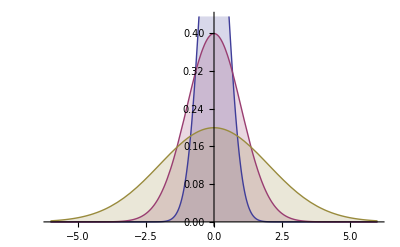

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{.5,1,2}}],{x,-6,6},Filling->Axis]
```

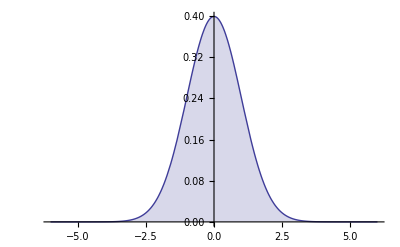

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,1}],{x,-6,6},Filling->Axis]
```

```mathematica
Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,1}]
```

{(ⅇ^(-x^2/2))/(√(2 π))}

```mathematica
Evaluate[%,{x=={.5,1,1.5,2}}]
```

Sequence[{(ⅇ^(-x^2/2))/(√(2 π))},{x=={0.5,1,1.5,2}}]

```mathematica
N[%]
```

N::arg: Argument {x == {0.5, 1, 1.5, 2}} is not of the form {precision, accuracy}.

N[{(ⅇ^(-x^2/2))/(√(2 π))},{x=={0.5,1,1.5,2}}]

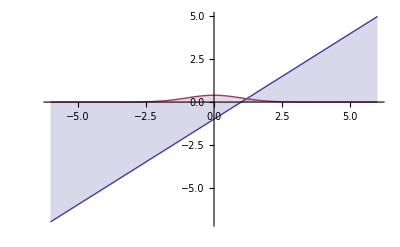

```mathematica
Plot[{x==1,Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,1}]},{x,-6,6},Filling->Axis]
```